```mathematica
g = 9.8;
l = .5;
omega = √(g/l);
θ0 = 20 * π/180;
ω0 = 0;

ode1 = {θ''[t] == - (g/l) * Sin[θ[t]], θ[0] == θ0, θ'[0] == ω0};
sol = NDSolve[ode1, θ, {t, 0, 20}];

approx = (180 / Pi) θ0 Cos[omega *t];
```

```mathematica
myplot = Plot[{approx, (180/Pi) θ[t] /. sol}, {t, 0, 20}, 
PlotStyle -> {{Blue}, {Dashed, Red}},
AxesLabel -> {"t (s)", "θ (rad)"},
PlotRange -> {{0, 10}, {-20,20}}, ImageSize -> {500, 300}];
```

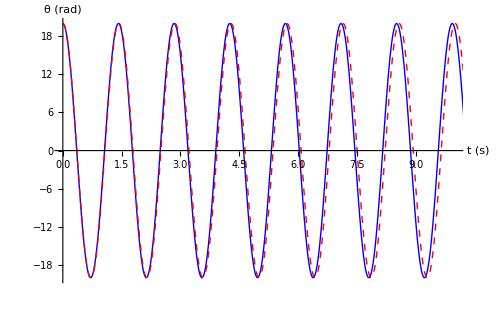

```mathematica
Show[myplot]
```